# Two-Species Lotka-Volterra Competition

The Lotka-Volterra competition model is one of the simplest competition models.  It is a logical extension of logistic growth to two competing species.

r1 and r2 are carrying capacities of species 1 and 2, and a12 and a21 are competition coefficients.

```mathematica
Needs["EcoEvo`"];
```

Set up the model:

```mathematica
SetModel[{
Pop[n1]->{Equation:>n1[t](r1-a11 n1[t]-a12 n2[t])},Pop[n2]->{Equation:>n2[t](r2-a21 n1[t]-a22 n2[t])},
Assumptions->{a12>0,a21>0,r1>0,r2>0}
}];
```

For simplicity, set a11=a22=1:

```mathematica
a11=a22=1;
```

First, find equilibria:

```mathematica
eq=SolveEcoEq[];
eq//NumberedGridForm
```

1 | {n1→0,n2→0}
2 | {n1→r1,n2→0}
3 | {n1→0,n2→r2}
4 | {n1→-(r1-a12 r2)/(-1+a12 a21),n2→-(-a21 r1+r2)/(-1+a12 a21)}

Now check linear stability of these equilibria with EcoEigenvalues:

```mathematica
FullSimplify[EcoEigenvalues[eq]]//NumberedGridForm
```

1 | {r1,r2}
2 | {-r1,-a21 r1+r2}
3 | {-r2,r1-a12 r2}
4 | {(r1-a21 r1+r2-a12 r2-√(((-1+a21) r1+(-1+a12) r2)^2+4 (-1+a12 a21) (a21 r1-r2) (-r1+a12 r2)))/(-2+2 a12 a21),(r1-a21 r1+r2-a12 r2+√(((-1+a21) r1+(-1+a12) r2)^2+4 (-1+a12 a21) (a21 r1-r2) (-r1+a12 r2)))/(-2+2 a12 a21)}

Or simply use EcoStableQ to find conditions for stability:

```mathematica
FullSimplify[EcoStableQ[eq]]//NumberedGridForm
```

1 | False
2 | Piecewise[{{True, a21 r1>r2}, {False, a21 r1<r2||r1+a21 r1<r2}, {Indeterminate, True}}]
3 | Piecewise[{{True, a12 r2>r1}, {False, a12 r2<r1||r2+a12 r2<r1}, {Indeterminate, True}}]
4 | Piecewise[{{True, (-1+a12 a21) ((-1+a21) r1+(-1+a12) r2)>0&&(-1+a12 a21) (a21 r1-r2) (-r1+a12 r2)<0}, {False, (-1+a12 a21) ((-1+a21) r1+(-1+a12) r2)<0||(-1+a12 a21) (a21 r1-r2) (-r1+a12 r2)>0}, {Indeterminate, True}}]

Calculate the invasibility of the single-species equilibria:

```mathematica
λ12=Inv[eq⟦3⟧,n1](* 1 invading 2 *) 
λ21=Inv[eq⟦2⟧,n2](* 2 invading 1 *)
```

r1-a12 r2

-a21 r1+r2

Notice that these correspond to one of the eigenvalues of the single-species equilibria calculated by EcoEigenvalues above.

Solve for critical values of r1 and r2:

```mathematica
Solve[λ12==0,r1]
Solve[λ21==0,r2]
```

{{r1→a12 r2}}

{{r2→a21 r1}}

Based on mutual invasibility, the outcome of competition is:

r1>a12 r2 && r2<a21 r1 | Case I - Species 1 outcompetes species 2
r1<a12 r2 && r2>a21 r1 | Case II - Species 2 outcompetes species 1
r1>a12 r2 && r2>a21 r1 | Case III - Species 1 & 2 coexist
r1<a12 r2 && r2<a21 r1 | Case IV - Founder control
r1==r2 && α12==α21 | Case 0 - Neutrality

Let's plot phase planes and simulate the model for all five of these cases.

### Case I - Species 1 outcompetes species 2

```mathematica
a12=a21=1;
r1=1.2;
r2=1;
```

Solve for equilibria:

```mathematica
SolveEcoEq[]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1→0,n2→0},{n1→1.2,n2→0},{n1→0,n2→1.}}

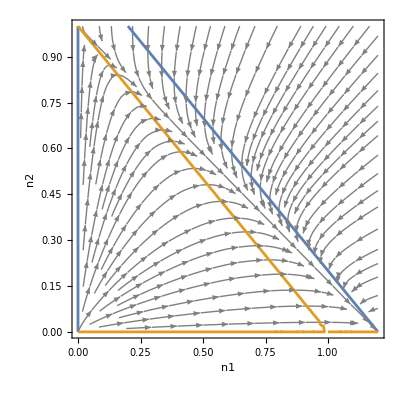

```mathematica
PlotEcoPhasePlane[{n1,0,r1},{n2,0,r2}]
```

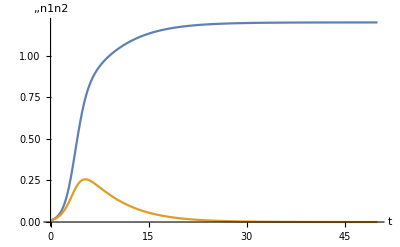

```mathematica
sol=EcoSim[{n1->0.01,n2->0.01},50];
PlotDynamics[sol]
```

### Case II - Species 2 outcompetes species 1

```mathematica
a12=a21=1;
r1=1;
r2=1.2;
```

Solve for equilibria:

```mathematica
SolveEcoEq[]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1→0,n2→0},{n1→1.,n2→0},{n1→0,n2→1.2}}

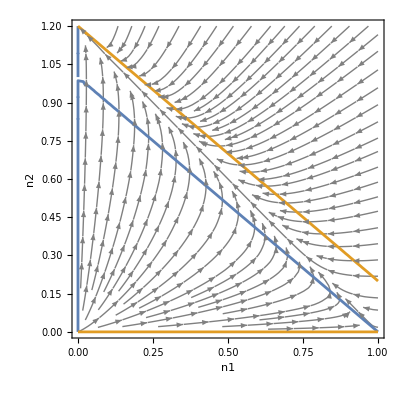

```mathematica
PlotEcoPhasePlane[{n1,0,r1},{n2,0,r2}]
```

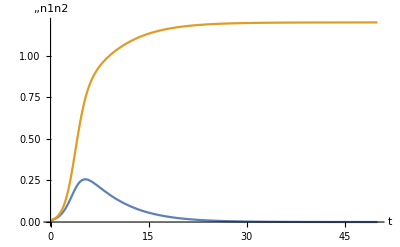

```mathematica
sol=EcoSim[{n1->0.01,n2->0.01},50];
PlotDynamics[sol]
```

### Case III - Species 1&2 coexist

```mathematica
a12=a21=0.5;
r1=1.2;
r2=1;
```

Solve for equilibria:

```mathematica
eq=SolveEcoEq[]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1→0,n2→0},{n1→1.2,n2→0},{n1→0,n2→1.},{n1→0.933333,n2→0.533333}}

Check stability of the coexistence equilibrium:

```mathematica
EcoEigenvalues[eq⟦4⟧]
```

{-1.13885,-0.327816}

Both eigenvalues are negative, so the coexistence equilibrium is stable:

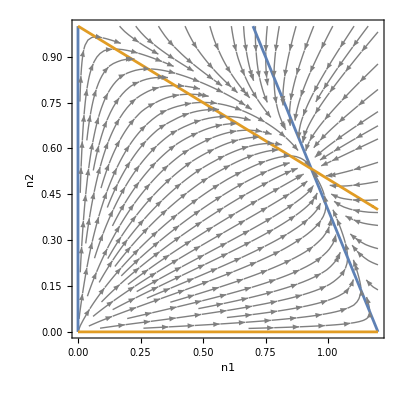

```mathematica
PlotEcoPhasePlane[{n1,0,r1},{n2,0,r2}]
```

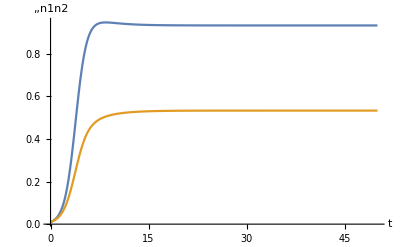

```mathematica
sol=EcoSim[{n1->0.01,n2->0.01},50];
PlotDynamics[sol]
```

### Case IV - Founder control

```mathematica
a12=a21=2;
r1=1;
r2=1;
```

Solve for equilibria:

```mathematica
eq=SolveEcoEq[]
```

{{n1→0,n2→0},{n1→1,n2→0},{n1→0,n2→1},{n1→1/3,n2→1/3}}

Check stability of the coexistence equilibrium.

```mathematica
EcoEigenvalues[eq⟦4⟧]
```

{-1,1/3}

One positive and one negative eigenvalue indicate that it is an unstable saddle point:

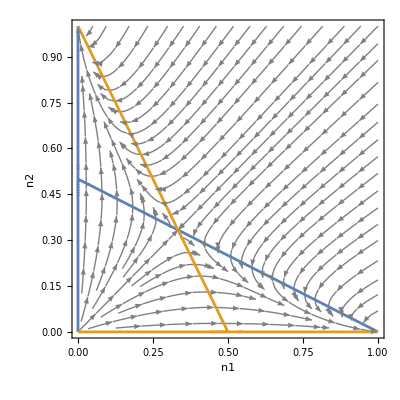

```mathematica
PlotEcoPhasePlane[{n1,0,r1},{n2,0,r2}]
```

Here the outcome depends on the initial conditions:

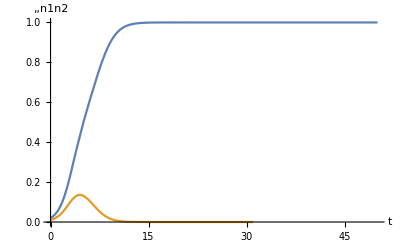

```mathematica
sol=EcoSim[{n1->0.02,n2->0.01},50];
PlotDynamics[sol]
```

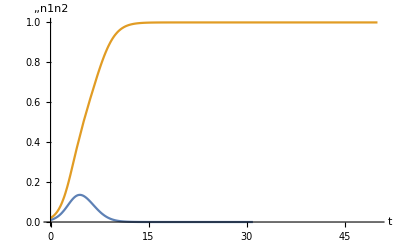

```mathematica
sol=EcoSim[{n1->0.01,n2->0.02},50];
PlotDynamics[sol]
```

### Case 0 - Neutrality

```mathematica
a12=a21=1;
r1=r2=1;
```

Solve for equilibria:

```mathematica
eq=SolveEcoEq[]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{n2→1-n1},{n1→0,n2→0}}

The first solution is a continuous range of neutrally stable equilibria, which we can verify with EcoEigenvalues:

```mathematica
EcoEigenvalues[eq⟦1⟧]
```

{-1,0}

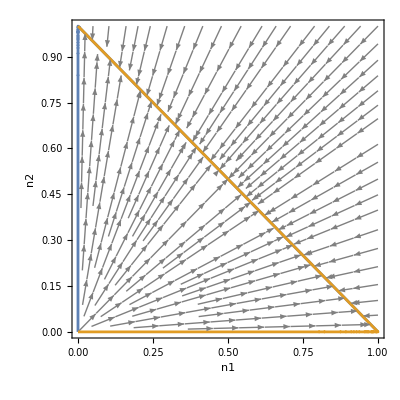

```mathematica
PlotEcoPhasePlane[{n1,0,r1},{n2,0,r2}]
```

Since there is a continuous range of neutrally stable equilibria, the outcome depends continuously on initial conditions:

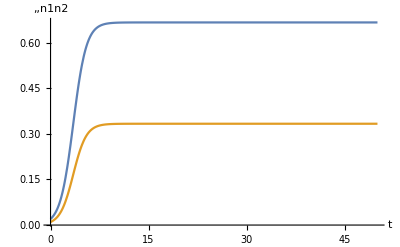

```mathematica
sol=EcoSim[{n1->0.02,n2->0.01},50];
PlotDynamics[sol]
```

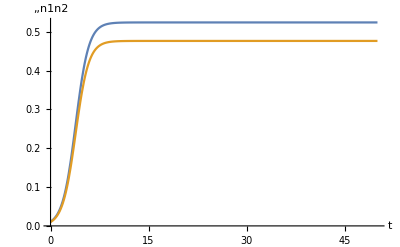

```mathematica
sol=EcoSim[{n1->0.011,n2->0.01},50];
PlotDynamics[sol]
```

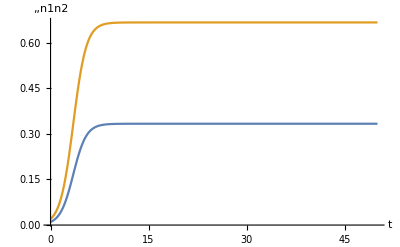

```mathematica
sol=EcoSim[{n1->0.01,n2->0.02},50];
PlotDynamics[sol]
```

## References

Related Tutorials

ExampleModels